```mathematica
EvaluateToStart = "EvaluateToStart"
```

EvaluateToStart

```mathematica
ClearAll["Global`*"]
```

# Master Peoject Notebook

## Dirac Basis

## Preparation to calculate Bogoliubov coefficients

## Matrices Definition

```mathematica
σ= {{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
σto={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}},{{0, 0, -I, 0}, {0, 0, 0, -I}, {I, 0, 0, 0}, {0, I, 0, 0}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}};

otτ={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}},{{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, -I}, {0, 0, I, 0}},{{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}};
τ = {ArrayFlatten[{{otτ[[1]],0},{0,otτ[[1]]}}],ArrayFlatten[{{otτ[[2]],0},{0,otτ[[2]]}}],ArrayFlatten[{{otτ[[3]],0},{0,otτ[[3]]}}],ArrayFlatten[{{otτ[[4]],0},{0,otτ[[4]]}}]};
{τ[[1]]//MatrixForm,τ[[2]]//MatrixForm,τ[[3]]//MatrixForm,τ[[4]]//MatrixForm};
γD = {ArrayFlatten[{{σto[[1]],0},{0,-σto[[1]]}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
{γD[[1]]//MatrixForm,γD[[2]]//MatrixForm,γD[[3]]//MatrixForm,γD[[4]]//MatrixForm};
```

## Finding EigenValues[] and EigenVectors[]

```mathematica
DiracHamiltonianD=M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}]);
AnsD=FullSimplify[Eigensystem[M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}])]];
ωD = Table[AnsD[[1]][[i]],{i,1,8}];
uD = Table[AnsD[[2]][[i]],{i,1,8}];
fωD[η_,k_]:={-1/2 √((-2 k+f[η])^2+4 M[η]^2),1/2 √((-2 k+f[η])^2+4 M[η]^2),-1/2 √((2 k+f[η])^2+4 M[η]^2),1/2 √((2 k+f[η])^2+4 M[η]^2),-1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),-1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))};
ωDc[k_,f_,M_]:= {-1/2 √((-2 k+f)^2+4 M^2),1/2 √((-2 k+f)^2+4 M^2),-1/2 √((2 k+f)^2+4 M^2),1/2 √((2 k+f)^2+4 M^2),-1/2 √(5 f^2+4 (k^2-√(f^2 (k^2+f^2))+M^2)),1/2 √(5 f^2+4 (k^2-√(f^2 (k^2+f^2))+M^2)),-1/2 √(5 f^2+4 (k^2+√(f^2 (k^2+f^2))+M^2)),1/2 √(5 f^2+4 (k^2+√(f^2 (k^2+f^2))+M^2))};
```

### Simplifying EigenVectors

```mathematica
suD=Table[0,{i,1,8}];
```

```mathematica
suD[[1]]=uD[[1]];
suD[[1]]=Simplify[uD[[1]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[1]]=√(ω1+M[η])suD[[1]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[1]]=suD[[1]]/.(√(ω1+M[η])(ω1-M[η]))/(√(ω1^2-M[η]^2))->√(ω1-M[η])
```

{(√(ω1-M[η]))/Sign[2 k-f[η]],0,0,0,√(ω1+M[η]),0,0,0}

```mathematica
suD[[2]]=Simplify[uD[[2]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[2]]=√(ω1-M[η])suD[[2]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[2]]=suD[[2]]/.((ω1+M[η])√(ω1-M[η]))/(√(ω1^2-M[η]^2))->√(ω1+M[η])
```

{-(√(ω1+M[η]))/Sign[2 k-f[η]],0,0,0,√(ω1-M[η]),0,0,0}

```mathematica
suD[[3]]=Simplify[uD[[3]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[3]]=√(ω2+M[η])suD[[3]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[3]]=suD[[3]]/.(√(ω2+M[η])(ω2-M[η]))/(√(ω2^2-M[η]^2))->√(ω2-M[η])
```

{0,0,0,-(√(ω2-M[η]))/Sign[2 k+f[η]],0,0,0,√(ω2+M[η])}

```mathematica
suD[[4]]=Simplify[uD[[4]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[4]]=√(ω2-M[η])suD[[4]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[4]]=suD[[4]]/.((ω2+M[η])√(ω2-M[η]))/(√(ω2^2-M[η]^2))->√(ω2+M[η])
```

{0,0,0,(√(ω2+M[η]))/Sign[2 k+f[η]],0,0,0,√(ω2-M[η])}

```mathematica
suD[[5]]=Simplify[uD[[5]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[5]]=√(ω3+M[η])suD[[5]]/.√(ω3+M[η]) (ω3-M[η])->√(ω3^2-M[η]^2)√(ω3-M[η]);
suD[[5]]=suD[[5]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=Simplify[suD[[5]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[5]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[5]]/.√(1/2 √(f[η]^2)+√(k^2+f[η]^2))√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[5]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[5]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));

suD[[5]]=suD[[5]]/.(2 f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=suD[[5]]/.(2 f[η])/(f[η]2-2  √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[5]]/.2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->-2/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[5]] =Assuming[k>0&&f[η]>0,FullSimplify[ suD[[5]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,-(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),-(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),0,0,(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),0}

```mathematica
suD[[6]]=Simplify[uD[[6]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[6]]=√(ω3-M[η])suD[[6]]/.√(ω3-M[η]) (ω3+M[η])->√(ω3^2-M[η]^2)√(ω3+M[η]);
suD[[6]]=suD[[6]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=Simplify[suD[[6]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[6]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[6]]/.√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) √(1/2 √(f[η]^2)+√(k^2+f[η]^2))->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[6]]=suD[[6]]/.(2(k f[η]-√(f[η]^2 (k^2+f[η]^2)))) ->-2(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) ;
suD[[6]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[6]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2* f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2* f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[6]]/.-2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->2/(2 √(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[6]] =  Assuming[k>0&&f[η]>0,FullSimplify[suD[[6]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),0,0,(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),0}

```mathematica
suD[[7]]=Simplify[uD[[7]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[7]]=√(ω4+M[η])suD[[7]]/.√(ω4+M[η]) (ω4-M[η])->√(ω4^2-M[η]^2)√(ω4-M[η]);
suD[[7]]=suD[[7]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=Simplify[suD[[7]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[7]]=suD[[7]]/.((k f[η]-√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/f[η]^2-> - ((-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/f[η]^2;
suD[[7]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[7]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[7]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[7]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=suD[[7]]/.(-2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[7]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[7]] =  Assuming[k>0&&f[η]>0,FullSimplify[suD[[7]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,-(√((k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),0,0,-(√((k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),0}

```mathematica
suD[[8]]=Simplify[uD[[8]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[8]]=√(ω4-M[η])suD[[8]]/.√(ω4-M[η]) (ω4+M[η])->√(ω4^2-M[η]^2)√(ω4+M[η]);
suD[[8]]=suD[[8]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=Simplify[suD[[8]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[8]]=suD[[8]]/.((k f[η]-√(f[η]^2 (k^2+f[η]^2))) √(ω4-M[η]))/f[η]^2->-((-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4-M[η]))/f[η]^2;
suD[[8]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[8]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[8]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[8]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=suD[[8]]/.(2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[8]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[8]] =  Assuming[k>0&&f[η]>0,FullSimplify[suD[[8]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,(√((k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),-(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),0,0,-(√((k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),0}

```mathematica
nsuD = suD;
nsuD[[1]] = 1/(√(2*ω1))*nsuD[[1]];
nsuD[[2]]= 1/(√(2*ω1))*nsuD[[2]];
nsuD[[3]] = 1/(√(2*ω2))*nsuD[[3]];
nsuD[[4]] = 1/(√(2*ω2))*nsuD[[4]];
nsuD[[5]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[5]];
nsuD[[6]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[6]];
nsuD[[7]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[7]];
nsuD[[8]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[8]];
```

```mathematica
Assuming[k>0&&f[η]>0&&ω3>M[η] && M[η]>0,FullSimplify[Norm[nsuD[[5]]]]]
```

1

```mathematica
Norm[nsuD[[5]]]
```

√(1/4 Abs[(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2+1/4 Abs[(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2+1/4 Abs[(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2+1/4 Abs[(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2)

### Check that simplifying went correct

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
 For[j=1,j<=i,j++,
  product = Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]];
  product=product/.Sign[2 k-f[η]]^2->1;
  product=product/.Sign[2 k+f[η]]^2->1;
  product=product/.√(ω3-M[η]) √(ω3+M[η])->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
  product=product/.√(f[η]^2) (k^2+f[η]^2)-√(k^2+f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.√(ω4-M[η]) √(ω4+M[η])->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
  product=product/.-f[η]^2 √(k^2+f[η]^2)+√(f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.ω3->1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.ω4->1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.√(-2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)));
         product=Simplify[product/.√(2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))];       
  product=product/.k f[η]-√(f[η]^2 (k^2+f[η]^2))+√(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->0;
         
If[i==j && (Assuming[k>0&&f[η]>0,product===0]) , errors++; Print[i,j, product]];  
  If[i!=j && !(Assuming[k>0&&f[η]>0,product===0]) , errors++;Print[i,j,product]];
]
]
If[errors==0,Print[True];];
If[errors!=0,Print[False];];
```

True

```mathematica
Table[ Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]],{i,1,8},{j,1,8}];
```

```mathematica
(* check that suD are proportional to uD*)
errors = 0;
For[i=1, i<=8, i++,
	multiplier=0;
	For[j=1,j<=8,j++,
		If[uD[[i]][[j]]===1,
			multiplier = suD[[i]][[j]];
		];
	];
	muD = multiplier* uD[[i]];
	For[j=1,j<=8,j++,
		If[suD[[i]][[j]]===0 && muD[[j]] != 0,
			Print["Error for: ",i,j];
			errors += 1;
		];
		If[!suD[[i]][[j]]===0,
			If[! Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]==1]],
				Print["Error for: ",i,j, "got:",Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]]], muD[[j]], uD[[i]][[j]]];
				errors+=1;
			];
		];
	]
]
If[errors == 0, Print[True],Print[False]]
```

True

## derivatives of eigenvectors, products of eigenvectors derivatives and eigenvectors

```mathematica
dnsuD= Table[D[nsuD[[i]],η],{i,1,8}];
```

### scalar product of eigenvectors and its derivatives

```mathematica
productsD=Table[Dot[nsuD[[i]],dnsuD[[j]]],{i,1,8},{j,1,8}];
productsD//MatrixForm;
productsD==Assuming[f[η]>0 && k >0&&M[η]>0, FullSimplify[productsD]];
```

### check that up and down do not mix

```mathematica
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
If[errors ==0, Print[True]]
```

True

```mathematica
productsD1 = Table[FullSimplify[productsD[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsD2 = Table[FullSimplify[productsD[[i]][[j]]],{i,3,4},{j,3,4}];
```

```mathematica
productsD3 = Table[FullSimplify[productsD[[i]][[j]]],{i,5,8},{j,5,8}];
```

#### Mixing of aup-up (assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD1 =Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0 && 2k!=f[η],FullSimplify[productsD1/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]
```

{{0,-M'[η]/(2 √(ω1^2-M[η]^2))},{M'[η]/(2 √(ω1^2-M[η]^2)),0}}

#### Mixing of adown-down(assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD2 =FullSimplify[Assuming[k>0&& M[η]>0&&ω2 > M[η]&&f[η]>0,FullSimplify[productsD2/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]/.Sign'[2 k+f[η]]->0]
```

{{0,-M'[η]/(2 √(ω2^2-M[η]^2))},{M'[η]/(2 √(ω2^2-M[η]^2)),0}}

### Mixed part

```mathematica
sproductsD3=Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0,FullSimplify[productsD3]]
```

{{0,-M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),0,(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),0,-M'[η]/(2 √(ω4-M[η]) √(ω4+M[η]))},{-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),M'[η]/(2 √(ω4-M[η]) √(ω4+M[η])),0}}

### Combine into one 8x8 matrix and then split into four 4x4 matrices

```mathematica
Combined=DiagonalMatrix[Hold/@{sproductsD1,sproductsD2,sproductsD3}]//ReleaseHold//ArrayFlatten;
Combined;
Combined = Combined /.ω1-> ωD[[2]]/.ω2-> ωD[[4]]/.ω3-> ωD[[6]]/.ω4-> ωD[[8]];fCombined[a_,b_]:=Combined/.η->a/.k->b
```

```mathematica
Combined//MatrixForm
```

(0 | -M'[η]/(2 √(-M[η]^2+1/4 ((-2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0 | 0 | 0
M'[η]/(2 √(-M[η]^2+1/4 ((-2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -M'[η]/(2 √(-M[η]^2+1/4 ((2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0
0 | 0 | M'[η]/(2 √(-M[η]^2+1/4 ((2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) | (k (-√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | (k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4))
0 | 0 | 0 | 0 | M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) | 0 | (k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | (k (√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))-√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4))
0 | 0 | 0 | 0 | (k (√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))-√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | -(k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | 0 | -M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))
0 | 0 | 0 | 0 | -(k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | (k (-√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) | 0)

### Dump to memory before defining f[t] and M[t]

```mathematica
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/ωD.mx",ωD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/uD.mx",uD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/nsuD.mx",nsuD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/dnsuD.mx",dnsuD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD1.mx",sproductsD1];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD2.mx",sproductsD2];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD3.mx",sproductsD3];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/Combined.mx",Combined];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fCombined.mx",fCombined];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fωD.mx",fωD];
```

## Bogoliubov coefficients calculation

### Get from memory

```mathematica
ClearAll["Global`*"]
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/ωD.mx",ωD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/uD.mx",uD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/nsuD.mx",nsuD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/dnsuD.mx",dnsuD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD1.mx",sproductsD1];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD2.mx",sproductsD2];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD3.mx",sproductsD3];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/Combined.mx",Combined];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fCombined.mx",fCombined];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fωD.mx",fωD];
```

### Define Matrices

```mathematica
a[η_]={{a11[η],a12[η],a13[η],a14[η]},{a21[η],a22[η],a23[η],a24[η]},{a31[η],a32[η],a33[η],a34[η]},{a41[η],a42[η],a43[η],a44[η]}};
b[η_]={{b11[η],b12[η],b13[η],b14[η]},{b21[η],b22[η],b23[η],b24[η]},{b31[η],b32[η],b33[η],b34[η]},{b41[η],b42[η],b43[η],b44[η]}};
amixed[η_]=Table[a[η][[i+2]][[j+2]],{i,1,2},{j,1,2}];
bmixed[η_]=Table[b[η][[i+2]][[j+2]],{i,1,2},{j,1,2}];
aup[η] = a[η][[1]][[1]];
bup[η] = b[η][[1]][[1]];
adown[η] = a[η][[2]][[2]];
bdown[η] = b[η][[2]][[2]];
(*phasesPlus[η1_]:=Table[Exp[2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]
phasesMinus[η1_]:=Table[Exp[-2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]*)
```

```mathematica
A1[η_,k_]:=Table[fCombined[η,k]⟦2 i⟧⟦2 j⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
A2[η_,k_]:=Table[fCombined[η,k]⟦2 i⟧⟦2 j-1⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
B1[η_,k_]:=Table[fCombined[η,k]⟦2 i-1⟧⟦2 j⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
B2[η_,k_]:=Table[fCombined[η,k]⟦2 i-1⟧⟦2 j-1⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
A1mixed[η_,k_]:= Table[A1[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
A2mixed[η_,k_]:= Table[A2[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
B1mixed[η_,k_]:= Table[B1[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
B2mixed[η_,k_]:= Table[B2[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
```

Take care of  infinities

```mathematica
ϵ = 0.000001;
AA2[η_,k_]:= Evaluate[Table[If[i==1&&j==1,0, A2[η,k][[i]][[j]]],{i,1,4},{j,1,4}]];
BB1[η_,k_]:= Evaluate[Table[If[i==1&&j==1,0, B1[η,k][[i]][[j]]],{i,1,4},{j,1,4}]];
A2[η_,k_,f1_]=Evaluate[Table[Piecewise[{{A2[η,k][[i]][[j]], (2k*η>-f1+ϵ ||2k*η<-f1-ϵ) && (2k*η>f1+ϵ ||2k*η<f1-ϵ)}, {AA2[η,k][[i]][[j]], True}}],{i,1,4},{j,1,4}]];
B1[η_,k_,f1_]=Evaluate[Table[Piecewise[{{B1[η,k][[i]][[j]], (2k*η>-f1+ϵ ||2k*η<-f1-ϵ) && (2k*η>f1+ϵ ||2k*η<f1-ϵ)}, {BB1[η,k][[i]][[j]], True}}],{i,1,4},{j,1,4}]];
A1up[η_,k_]:= A1[η,k][[1]][[1]]
A2up[η_,k_,f1_]:= A2[η,k,f1][[1]][[1]]
B1up[η_,k_,f1_]:= B1[η,k,f1][[1]][[1]]
B2up[η_,k_]:= B2[η,k][[1]][[1]]
A1down[η_,k_]:= A1[η,k][[2]][[2]]
A2down[η_,k_,f1_]:= A2[η,k,f1][[2]][[2]]
B1down[η_,k_,f1_]:= B1[η,k,f1][[2]][[2]]
B2down[η_,k_]:= B2[η,k][[2]][[2]]
```

```mathematica
Ph[η_] = {Ph1[η],Ph2[η],Ph3[η],Ph4[η]};
ExpPhPlus[η_]={Exp[2*I*Ph1[η]],Exp[2*I*Ph2[η]],Exp[2*I*Ph3[η]],Exp[2*I*Ph4[η]]};
ExpPhMinus[η_]={Exp[-2*I*Ph1[η]],Exp[-2*I*Ph2[η]],Exp[-2*I*Ph3[η]],Exp[-2*I*Ph4[η]]};
ExpPhPlusMixed[η_]={Exp[2*I*Ph3[η]],Exp[2*I*Ph4[η]]};
ExpPhMinusMixed[η_]={Exp[-2*I*Ph3[η]],Exp[-2*I*Ph4[η]]};
```

```mathematica
Fstart = -2;
Fstop = -0.02;
f[η_]:=Piecewise[{{F1/2, η<=Fstart}, {-F1/η, Fstart<η<=Fstop}, {F1/0.02, Fstop<η}}];
df[η_]:=Piecewise[{{0, η<=Fstart}, {F1/η^2, Fstart<η<Fstop}, {0, Fstop<=η}}];
M[η_]:=-M1/η;
```

```mathematica
fsol[k_,m1_,f1_,start_,stop_] := NDSolve[{
a'[η]==a[η].Transpose[A1[η,k]] + Transpose[ExpPhPlus[η]*Transpose[b[η].Transpose[B1[η,k,f1]]]],
b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].Transpose[A2[η,k,f1]]]]+ b[η].Transpose[B2[η,k]],
Ph1'[η]==fωD[η,k][[2]],Ph2'[η]==fωD[η,k][[4]],Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},
Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1,
{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},
{η,start,stop}];
fsolmixedWithInit[k_,m1_,f1_,start_,stop_]:= NDSolve[{
amixed'[η]==amixed[η].Transpose[A1mixed[η,k]] + ExpPhPlusMixed[η]*bmixed[η].Transpose[B1mixed[η,k]],
bmixed'[η]== ExpPhMinusMixed[η]*amixed[η].Transpose[A2mixed[η,k]]+ bmixed[η].Transpose[B2mixed[η,k]],
Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
amixed[start]=={{1,0},{0,1}},
bmixed[start]=={{0,0},{0,0}},
Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1/.Fstart->start/.Fstop->stop,
{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
fsolmixedWithInit[k_,m1_,f1_,start_,stop_,ai_,bi_]:= NDSolve[{
amixed'[η]==amixed[η].Transpose[A1mixed[η,k]] + ExpPhPlusMixed[η]*bmixed[η].Transpose[B1mixed[η,k]],
bmixed'[η]== ExpPhMinusMixed[η]*amixed[η].Transpose[A2mixed[η,k]]+ bmixed[η].Transpose[B2mixed[η,k]],
Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
amixed[start]==ai,
bmixed[start]==bi,
Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1/.Fstart->start/.Fstop->stop,
{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
fsolup[k_,m1_,f1_,start_,stop_]:= NDSolve[{
a11'[η]==a11[η]*A1up[η,k] + ExpPhPlus[η][[1]]*b11[η]*B1up[η,k,f1],
b11'[η]== ExpPhMinus[η][[1]]*a11[η]*A2up[η,k,f1]+ b11[η]*B2up[η,k],
Ph1'[η]==fωD[η,k][[2]],
a11[start]==1,
b11[start]==0,
Ph1[start]==0}/.M1->m1/.F1->f1/.Fstart->start/.Fstop->stop,
{a11[η],b11[η],Ph1[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
fsoldown[k_,m1_,f1_,start_,stop_]:= NDSolve[{
a22'[η]==a22[η]*A1down[η,k] + ExpPhPlus[η][[2]]*b22[η]*B1down[η,k,f1],
b22'[η]== ExpPhMinus[η][[2]]*a22[η]*A2down[η,k,f1]+ bd22[η]*B2down[η,k],
Ph2'[η]==fωD[η,k][[4]],
a22[start]==1,
b22[start]==0,
Ph2[start]==0}/.M1-m1/.F1->f1/.Fstart->start/.Fstop->stop,
{a22[η],b22[η],Ph2[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
```

### No-mass check

```mathematica
maxN=50;
minN=-10;
f1=5;
m1=0;
Start=-20;
Stop = -2;
```

```mathematica
NN[n_]:= Piecewise[{{10.4^(1+3*(n/maxN)^3), n>=0}, {10.4^(1+3*(-n/minN)^3), n<0}}];
noMkdependence =Table[{NN[n]/f1,Evaluate[{Abs[a33[η]],Abs[a34[η]],Abs[a43[η]],Abs[a44[η]],Abs[b33[η]],Abs[b34[η]],Abs[b43[η]],Abs[b44[η]]}/.fsolmixed[NN[n],m1,f1,Start,Stop,{{1,0},{0,1}},{{0,0},{0,0}}]/.η->Stop][[1]]},{n,minN,maxN}];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/noMkdependence.mx",noMkdependence];
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/noMkdependence.mx",noMkdependence];
noMkdependencePlot = Table[ListLogLogPlot[Table[{noMkdependence[[n]][[1]],√2 noMkdependence[[n]][[2]][[j]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,8}];
```

```mathematica
aa=LogLogPlot[0.02,{x,0.01,1000}];
```

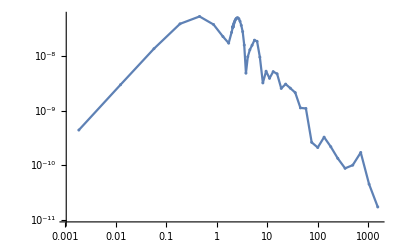

```mathematica
Show[noMkdependencePlot[[7]],aa]
```

## Solve for Bogoliubov coefficients

```mathematica
maxN=200;
minN=-100;
f1=5;
m1={0,10,50};
Start=-2;
Stop = -0.02;
NN[n_]:= Piecewise[{{10.4^(1+3*(n/maxN)^3), n>=0}, {10.4^(1+3*(-n/minN)^3), n<0}}];
```

```mathematica
kdependence = Table[Table[{NN[n]/f1,Evaluate[{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η]}/.fsolmixed[NN[n],m1[[i]],f1,Start,Stop,{{1,0},{0,1}},{{0,0},{0,0}}]/.η->Stop][[1]]},{n,minN,maxN}],{i,1,Length[m1]}];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependence.mx",kdependence];
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependence.mx",kdependence];
kdependencePlot = Table[Table[ListLogLinearPlot[Table[{kdependence[[i]][[n]][[1]],Abs[kdependence[[i]][[n]][[2]][[j]]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,8}],{i,1,Length[m1]}];
```

```mathematica
Manipulate[kdependencePlot[[i]],{i,1,Length[m1],1}]
```

Part::partd: Part specification kdependencePlot⟦1⟧ is longer than depth of object.

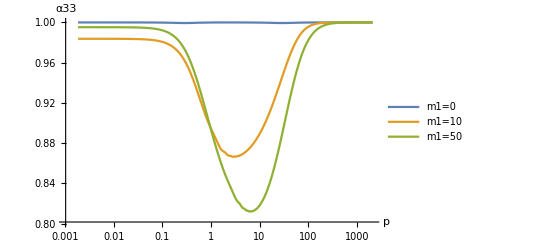
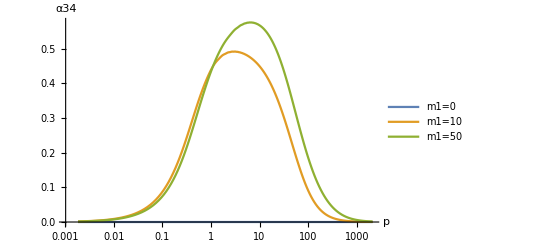
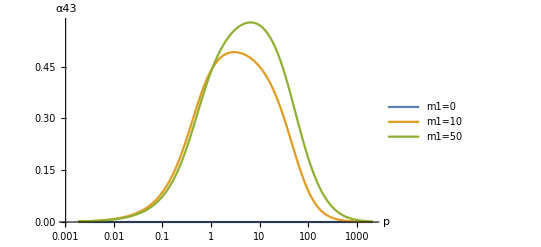
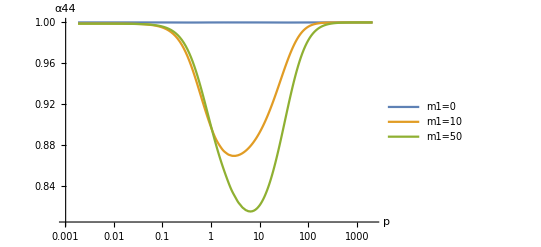
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
AlphaPlots=Table[ListLogLinearPlot[Table[Table[{kdependence[[i]][[n]][[1]],Abs[kdependence[[i]][[n]][[2]][[If[j2==1,j1,2+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m1=0","m1=10","m1=50"},AxesLabel->{p,ToString[α]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
```

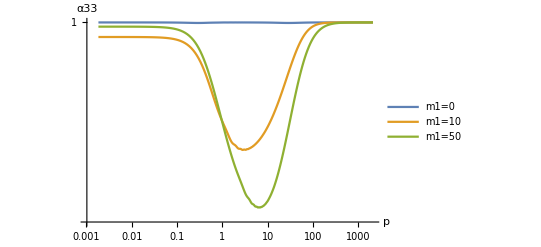
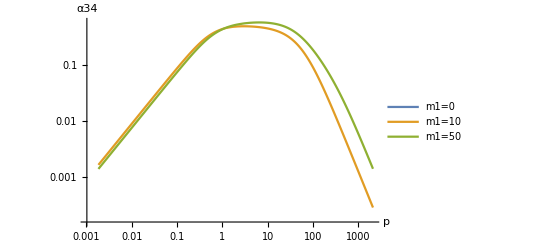
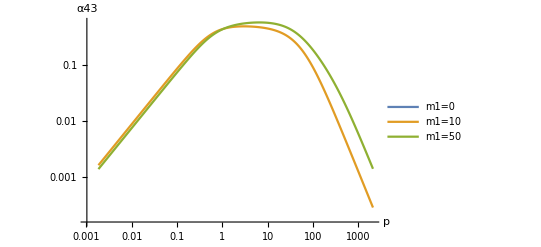
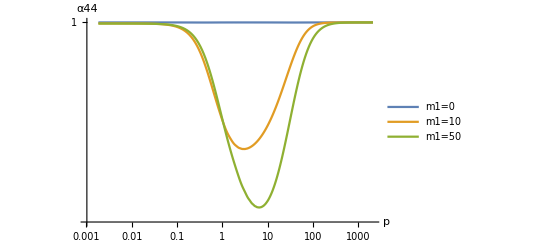
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
AlphaLogPlots=Table[ListLogLogPlot[Table[Table[{kdependence[[i]][[n]][[1]],Abs[kdependence[[i]][[n]][[2]][[If[j2==1,j1,2+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m1=0","m1=10","m1=50"},AxesLabel->{p,ToString[α]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
```

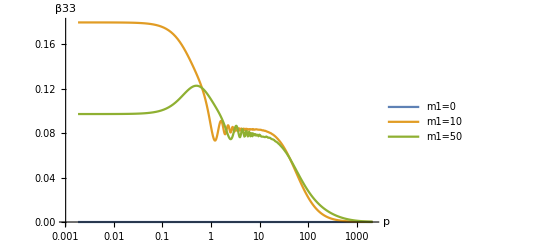
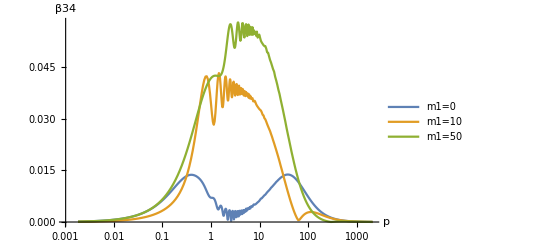
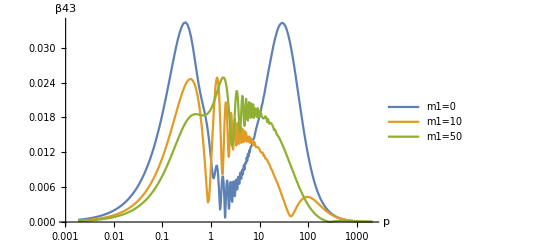
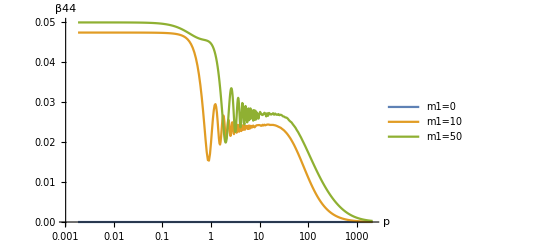
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
BetaPlots=Table[ListLogLinearPlot[Table[Table[{kdependence[[i]][[n]][[1]],Abs[kdependence[[i]][[n]][[2]][[If[j2==1,4+j1,6+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m1=0","m1=10","m1=50"},AxesLabel->{p,ToString[β]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
```

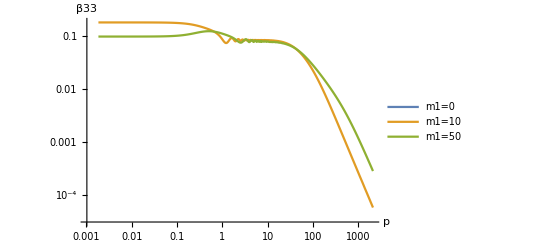
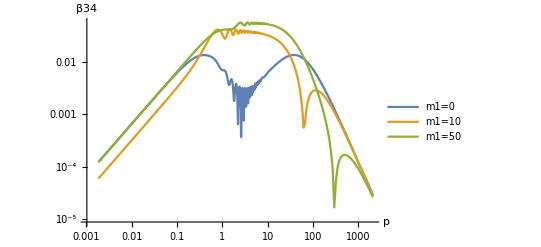
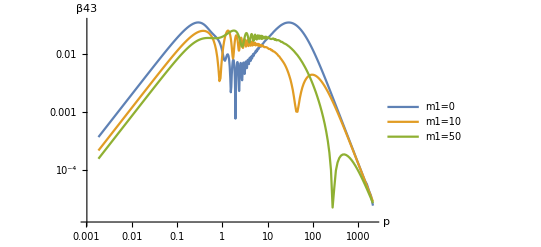
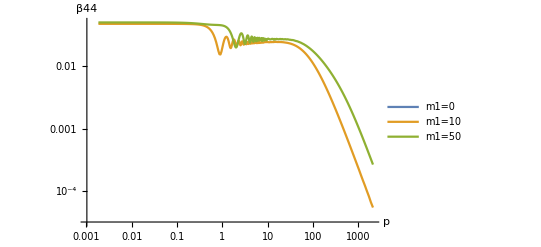
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
BetaLogPlots=Table[ListLogLogPlot[Table[Table[{kdependence[[i]][[n]][[1]],Abs[kdependence[[i]][[n]][[2]][[If[j2==1,4+j1,6+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m1=0","m1=10","m1=50"},AxesLabel->{p,ToString[β]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
```

```mathematica
ToString[1+2]<>"a"
```

3a

```mathematica
Table[ListPlot[{{kdependence[[1]][[n]][[1]],Abs[kdependence[[i]][[n]][[2]][[j]]]},{kdependence[[i]][[n]][[1]],Abs[kdependence[[1]][[n]][[2]][[j]]]}}]]
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependence.mx",kdependence];
AlphaMixed = Table[Table[{{kdependence[[i]][[n]][[2]][[1]],kdependence[[i]][[n]][[2]][[2]]},{kdependence[[i]][[n]][[2]][[3]],kdependence[[i]][[n]][[2]][[4]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];BetaMixed = Table[Table[{{kdependence[[i]][[n]][[2]][[5]],kdependence[[i]][[n]][[2]][[6]]},{kdependence[[i]][[n]][[2]][[7]],kdependence[[i]][[n]][[2]][[8]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixed = Table[Table[AlphaMixed[[i]][[n]].ConjugateTranspose[ AlphaMixed[[i]][[n]]]+Conjugate[BetaMixed[[i]][[n]]].Transpose[BetaMixed[[i]][[n]]],{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixedPlot = Table[Table[ListLogLinearPlot[Table[{kdependence[[i]][[n]][[1]],Abs[NormConditionMixed[[i]][[n]][[j]][[k]]]-1},{n,1,maxN-minN}], Joined->True, PlotRange->All],{j,1,2},{k,1,2}],{i,1,Length[m1]}];
Manipulate[Show[NormConditionMixedPlot[[i]][[1]][[1]],NormConditionMixedPlot[[i]][[2]][[2]],PlotRange->All],{i,1,Length[m1],1}]
```

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

```mathematica
maxN=200;
minN=-100;
NN[n_]:= Piecewise[{{10.4^(1+3*(n/maxN)^3), n>=0}, {10.4^(1+3*(-n/minN)^3), n<0}}];
kdependenceDown = Table[{NN[n]/f1,Evaluate[{a22[η],b22[η]}/.fsoldown[NN[n]]/.η->stop][[1]]},{n,minN,maxN}];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceDown.mx",kdependenceDown];
```

ReplaceAll::reps: {fsoldown[0.00924556]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {fsoldown[0.0113908]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
maxN=200;
minN=-100;
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceDown.mx",kdependenceDown];
kdependencePlotDown = Table[ListLogLogPlot[Table[{kdependenceDown[[n]][[1]],Abs[kdependenceDown[[n]][[2]][[j]]]},{n,1,maxN-minN}],PlotRange->{{10^-3,2*10^3},{10^-4, 10^-0}},PlotMarkers->{Automatic,3}, Joined->True],{j,1,2}]
```

{-Graphics-,-Graphics-}

```mathematica
NormConditionDown = Table[Abs[kdependenceDown[[n]][[2]][[1]]]^2+Abs[kdependenceDown[[n]][[2]][[2]]]^2,{n,1,maxN-minN}];
NormConditionDownPlot = ListLogLogPlot[Table[{kdependence[[n]][[1]],NormConditionDown[[n]]},{n,1,maxN-minN}], Joined->True, PlotRange->All]
```

Part::partw: Part 4 of {{{0.00184911,{1.-3.29863×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-1.13495×10^-7 ⅈ,0.+0. ⅈ,-0.0000684208+0.000358019 ⅈ,8.00642×10^-6-0.000121483 ⅈ,0.+0. ⅈ}},{0.00227816,{1.-5.00693×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-1.72236×10^-7 ⅈ,0.+0. ⅈ,-0.0000842931+0.000441085 ⅈ,9.95028×10^-6-0.000149686 ⅈ,0.+0. ⅈ}},«7»,{0.0104434,{0.999998-0.0000105165 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-3.61734×10^-6 ⅈ,0.+0. ⅈ,-0.000385538+0.0020208 ⅈ,0.000045479-0.000685786 ⅈ,0.+0. ⅈ}},«291»},«1»,{«1»}} does not exist.

Part::partw: Part 5 of {{{0.00184911,{1.-3.29863×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-1.13495×10^-7 ⅈ,0.+0. ⅈ,-0.0000684208+0.000358019 ⅈ,8.00642×10^-6-0.000121483 ⅈ,0.+0. ⅈ}},{0.00227816,{1.-5.00693×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-1.72236×10^-7 ⅈ,0.+0. ⅈ,-0.0000842931+0.000441085 ⅈ,9.95028×10^-6-0.000149686 ⅈ,0.+0. ⅈ}},«7»,{0.0104434,{0.999998-0.0000105165 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-3.61734×10^-6 ⅈ,0.+0. ⅈ,-0.000385538+0.0020208 ⅈ,0.000045479-0.000685786 ⅈ,0.+0. ⅈ}},«291»},«1»,{«1»}} does not exist.

Part::partw: Part 6 of {{{0.00184911,{1.-3.29863×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-1.13495×10^-7 ⅈ,0.+0. ⅈ,-0.0000684208+0.000358019 ⅈ,8.00642×10^-6-0.000121483 ⅈ,0.+0. ⅈ}},{0.00227816,{1.-5.00693×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-1.72236×10^-7 ⅈ,0.+0. ⅈ,-0.0000842931+0.000441085 ⅈ,9.95028×10^-6-0.000149686 ⅈ,0.+0. ⅈ}},«7»,{0.0104434,{0.999998-0.0000105165 ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-3.61734×10^-6 ⅈ,0.+0. ⅈ,-0.000385538+0.0020208 ⅈ,0.000045479-0.000685786 ⅈ,0.+0. ⅈ}},«291»},«1»,{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

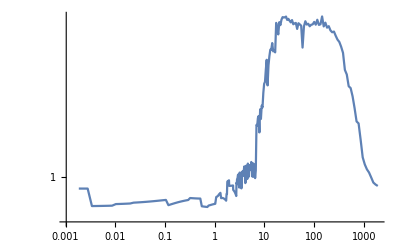
```mathematica
Solv-Graphics-
```

```mathematica
maxN=200;
minN=-100;
NN[n_]:= Piecewise[{{10.4^(1+3*(n/maxN)^3), n>=0}, {10.4^(1+3*(-n/minN)^3), n<0}}];
kdependenceUp = Table[{NN[n]/f1,Evaluate[{a11[η],b11[η]}/.fsolup[NN[n]]/.η->stop][[1]]},{n,minN,maxN}];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceUp.mx",kdependenceUp];
```

InterpolatingFunction::dmval: Input value {-0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

$Aborted[]

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,41.6079} is not a list of numbers with dimensions {3} at {η,a11[η],b11[η],Ph1[η],NDSolve`s$2381268[η],NDSolve`s$2381263[η],NDSolve`s$2381264[η],NDSolve`s$2381265[η]} = {-0.240339,-2.36409-4.28193 ⅈ,4.76047+0.70656 ⅈ,26.3786+0. ⅈ,-1,1,-1,1}.

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,41.6079} is not a list of numbers with dimensions {3} at {η,a11[η],b11[η],Ph1[η],NDSolve`s$2381962[η],NDSolve`s$2381957[η],NDSolve`s$2381958[η],NDSolve`s$2381959[η]} = {-0.240339,-2.36409-4.28193 ⅈ,4.76047+0.70656 ⅈ,26.3786+0. ⅈ,-1,1,-1,1}.

InterpolatingFunction::dmval: Input value {-0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,41.6079} is not a list of numbers with dimensions {3} at {η,a11[η],b11[η],Ph1[η],NDSolve`s$2382336[η],NDSolve`s$2382331[η],NDSolve`s$2382332[η],NDSolve`s$2382333[η]} = {-0.240339,-2.36409-4.28193 ⅈ,4.76047+0.70656 ⅈ,26.3786+0. ⅈ,-1,1,-1,1}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√0.) encountered.

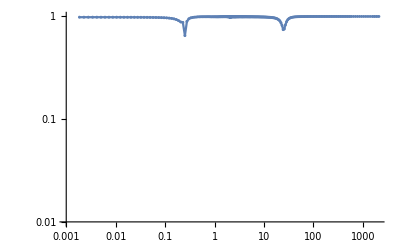
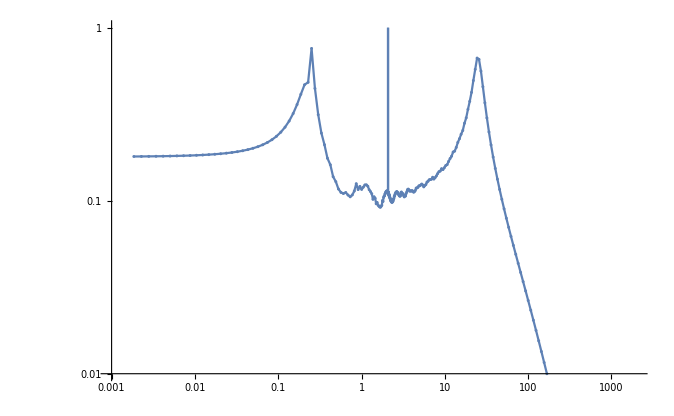

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceUp.mx",kdependenceUp];
kdependenceUpPlot = Table[ListLogLogPlot[Table[{kdependenceUp[[n]][[1]],Abs[kdependenceUp[[n]][[2]][[j]]]},{n,1,maxN-minN}],PlotRange->{{10^-3,2*10^3},{10^-2, 1}},PlotMarkers->{Automatic,3}, Joined->True],{j,1,2}]
```

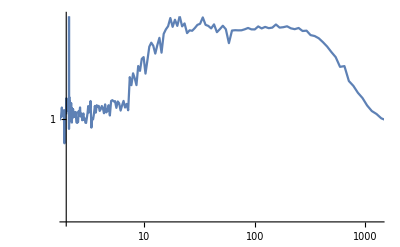

```mathematica
NormConditionUp = Table[Abs[kdependenceUp[[n]][[2]][[1]]]^2+Abs[kdependenceUp[[n]][[2]][[2]]]^2,{n,1,maxN-minN}];
NormConditionUpPlot = ListLogLogPlot[Table[{kdependence[[n]][[1]],NormConditionUp[[n]]},{n,1,maxN-minN}], Joined->True, PlotRange->{{0,1300},{0.999999, 1.000001}}]
```

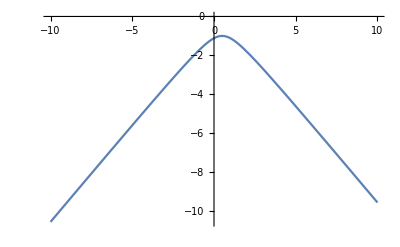

```mathematica
Plot[ωDc[k,1,1][[1]],{k,-10,10}]
```

```mathematica
Manipulate[Plot[Evaluate[ωDc[k,f,0.5]],{k,0,170},PlotLabel->t,PlotTheme->NeonColor,PlotRange->Automatic],{f,0,100}]
```

```mathematica
N[10^(1/8)]
```

```mathematica
1.333521432163324^2
```

1.77828

# Artifacts

```mathematica
fconnect2[x_,a_,b_]:=1/(2 a^2(a-b))(x-b)^2;
ϵ1=0.1;
ϵ2 = 0.001;
a1 = - 2-ϵ1;
b1   = -2+ϵ1;
a2 = - 0.02-ϵ2;
b2   = -0.02+ϵ2;
ff[η_]:=Piecewise[{
{f1*(-fconnect2[b1,b1,a1])+-f1/b1-f2, η< a1},
 {f1*(fconnect2[η,b1,a1]-fconnect2[b1,b1,a1])+-f1/b1-f2,a1<=η< b1},
{-f1/η -f2, b1<= η<a2},
{f1*(fconnect2[η,a2,b2]-fconnect2[a2,a2,b2]) + -f1/a2 -f2 ,a2<=η<b2},
{-f1/a2 -f2 - f1*fconnect2[a2,a2,b2], η>=b2}
},{η,start*2,0} ]; (*Make it picewise*)
```

```mathematica
konrad = Table[Table[{i,j},{i,1,2}],{j,1,2}]
```

{{{1,1},{2,1}},{{1,2},{2,2}}}

```mathematica
konrad[[1]][[2]]
```

{2,1}

```mathematica
fsolmixedtest[k_,m1_,f1_,start_,stop_]:= NDSolve[{
amixed'[η]==amixed[η].A1mixed[η,k] + bmixed[η].B1mixed[η,k],
bmixed'[η]== amixed[η].A2mixed[η,k]+ bmixed[η].B2mixed[η,k],
amixed[start]=={{1,0},{0,1}},
bmixed[start]=={{0,0},{0,0}}}/.M1->m1/.F1->f1/.Fstart->start/.Fstop->stop,
{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
```

```mathematica
maxN=50;
minN=-20;
f1=5;
m1=0;
Start=-2;
Stop = Start/100;
```

```mathematica
NN[n_]:= Piecewise[{{10.4^(1+3*(n/maxN)^3), n>=0}, {10.4^(1+3*(-n/minN)^3), n<0}}];
testNoMkdependence =Table[{NN[n]/f1,Evaluate[{Abs[a33[η]],Abs[a34[η]],Abs[a43[η]],Abs[a44[η]],Abs[b33[η]],Abs[b34[η]],Abs[b43[η]],Abs[b44[η]]}/.fsolmixedtest[NN[n],1,f1,Start,Stop]/.η->Stop][[1]]},{n,minN,maxN}];
```

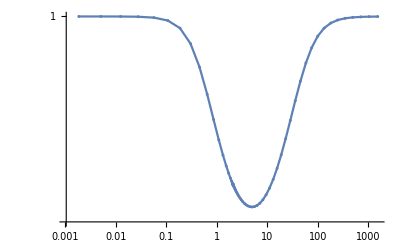
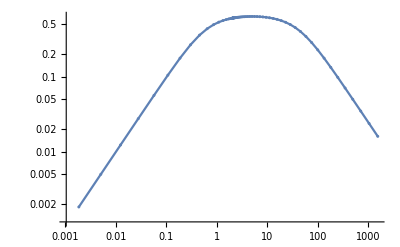
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
testNoMkdependencePlot = Table[ListLogLogPlot[Table[{testNoMkdependence[[n]][[1]],testNoMkdependence[[n]][[2]][[j]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,8}];
a=LogLogPlot[0.02,{x,0.01,1000}];
testNoMkdependencePlot
```

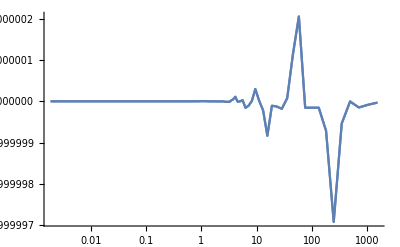

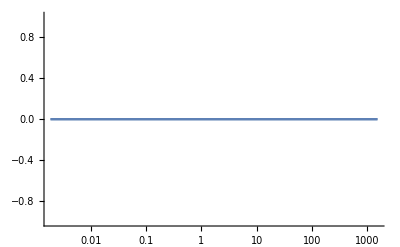

```mathematica
noMAlphaMixed = Table[{{testNoMkdependence[[n]][[2]][[1]],testNoMkdependence[[n]][[2]][[2]]},{testNoMkdependence[[n]][[2]][[3]],testNoMkdependence[[n]][[2]][[4]]}},{n,1,maxN-minN}];noMBetaMixed = Table[{{testNoMkdependence[[n]][[2]][[5]],testNoMkdependence[[n]][[2]][[6]]},{testNoMkdependence[[n]][[2]][[7]],testNoMkdependence[[n]][[2]][[8]]}},{n,1,maxN-minN}];
noMNormConditionMixed = Table[ noMAlphaMixed[[n]].ConjugateTranspose[noMAlphaMixed[[n]]]+Conjugate[noMBetaMixed[[n]]].Transpose[noMBetaMixed[[n]]],{n,1,maxN-minN}];
noMNormConditionMixed2 = Table[ noMAlphaMixed[[n]].ConjugateTranspose[noMAlphaMixed[[n]]],{n,1,maxN-minN}];
noMNormConditionMixedPlot=Table[ ListLogLinearPlot[Table[{testNoMkdependence[[n]][[1]],Re[noMNormConditionMixed[[n]][[i]][[j]]]},{n,1,maxN-minN}], Joined->True, PlotRange->All],{i,1,2},{j,1,2}];
noMNormConditionMixedPlot2=Table[ ListLogLinearPlot[Table[{testNoMkdependence[[n]][[1]],Re[noMNormConditionMixed2[[n]][[i]][[j]]]},{n,1,maxN-minN}], Joined->True, PlotRange->All],{i,1,2},{j,1,2}];
Show[noMNormConditionMixedPlot[[1]][[1]],noMNormConditionMixedPlot[[2]][[2]],PlotRange->All]
Show[noMNormConditionMixedPlot[[1]][[2]],noMNormConditionMixedPlot[[2]][[1]],PlotRange->All]
```

```mathematica
ω11[k_,f_,M_]:=ωDc[k,f,M][[2]];
ω22[k_,f_,M_]:=ωDc[k,f,M][[4]];
ω33[k_,f_,M_]:=ωDc[k,f,M][[6]];
ω44[k_,f_,M_]:=ωDc[k,f,M][[8]];
```

```mathematica
fM={{,},{,},{,}};
```

```mathematica
fM[[1]][[1]]=Plot[{ω11[k,2,0],ω22[k,2,0],ω33[k,2,0],ω44[k,2,0]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p","ω_p^j(f=2, M=0)"},ImageSize->Medium];
fM[[1]][[2]]=Plot[{ω11[k,4,0],ω22[k,4,0],ω33[k,4,0],ω44[k,4,0]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p","ω_p^j(f=4, M=0)"},ImageSize->Medium];
fM[[2]][[1]]=Plot[{ω11[k,2,2],ω22[k,2,2],ω33[k,2,2],ω44[k,2,2]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p","ω_p^j(f=2, M=2)"},ImageSize->Medium];
fM[[2]][[2]]=Plot[{ω11[k,4,2],ω22[k,4,2],ω33[k,4,2],ω44[k,4,2]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p","ω_p^j(f=4, M=2)"},ImageSize->Medium];
fM[[3]][[1]]=Plot[{ω11[k,2,2],ω22[k,2,2],ω33[k,2,2],ω44[k,2,2]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p","ω_p^j(f=2, M=2)"},ImageSize->Medium];
fM[[3]][[2]]=Plot[{ω11[k,4,2],ω22[k,4,2],ω33[k,4,2],ω44[k,4,2]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p","ω_p^j(f=4, M=2)"},ImageSize->Medium];
```

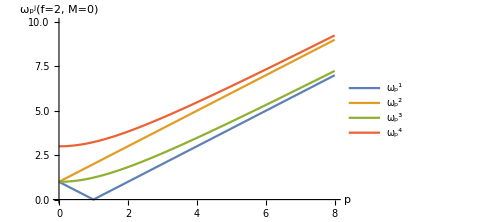
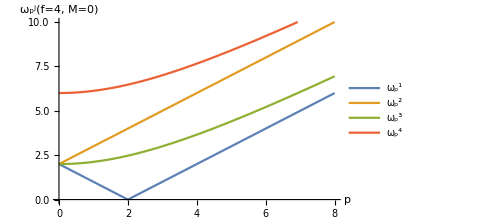
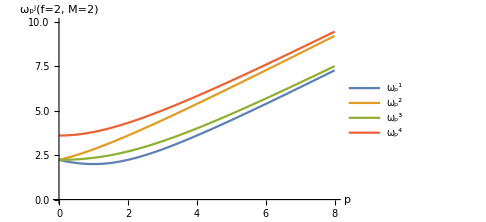
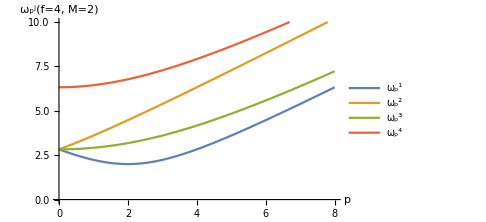
(-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
fM //MatrixForm
```

```mathematica
TableForm[%1257]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

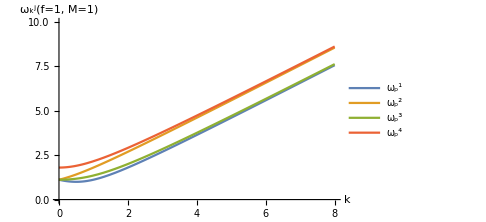
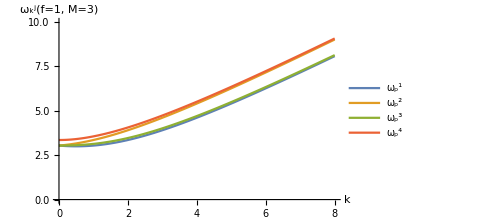
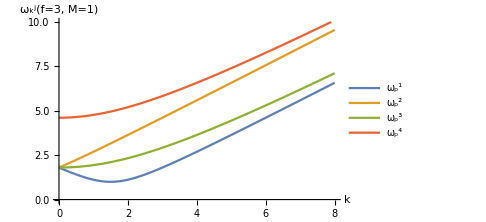
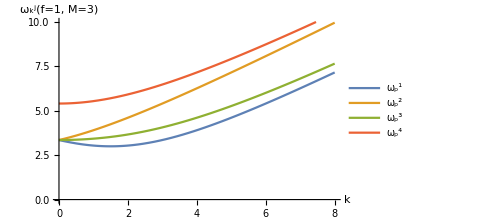
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TableForm[%1180]
```

```mathematica
γ5D = I *γD[[1]].γD[[2]].γD[[3]].γD[[4]];
```

```mathematica
PL = (IdentityMatrix[8]-γ5D)/2;
PR = (IdentityMatrix[8]+γ5D)/2;
```

```mathematica
PL + PR
```

{{(1-γ5D)/2+(1+γ5D)/2,0,0,0,0,0,0,0},{0,(1-γ5D)/2+(1+γ5D)/2,0,0,0,0,0,0},{0,0,(1-γ5D)/2+(1+γ5D)/2,0,0,0,0,0},{0,0,0,(1-γ5D)/2+(1+γ5D)/2,0,0,0,0},{0,0,0,0,(1-γ5D)/2+(1+γ5D)/2,0,0,0},{0,0,0,0,0,(1-γ5D)/2+(1+γ5D)/2,0,0},{0,0,0,0,0,0,(1-γ5D)/2+(1+γ5D)/2,0},{0,0,0,0,0,0,0,(1-γ5D)/2+(1+γ5D)/2}}

```mathematica
Assuming[k>0&&f[η]>0&& M[η]>0&& ω3>M[η],FullSimplify[Dot[PL.nsuD[[6]],nsuD[[6]]]]]
```

(ω3-√(ω3^2-M[η]^2))/(2 ω3)

```mathematica
MM=5;
FF=5;
Dot[nsuD[[6]],PR.nsuD[[6]]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02;
```

```mathematica
PR6[k_]:=Evaluate[Dot[nsuD[[6]],(PR.nsuD[[6]])/Norm[PR.nsuD[[6]]]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
PL6[k_]:=Evaluate[Dot[nsuD[[6]],(PL.nsuD[[6]])/Norm[PL.nsuD[[6]]]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
PR8[k_]:=Evaluate[Dot[nsuD[[8]],(PR.nsuD[[8]])/Norm[PR.nsuD[[8]]]]/.ω4->ωDc[k,MM/η,FF/η][[8]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
PL8[k_]:=Evaluate[Dot[nsuD[[8]],(PL.nsuD[[8]])/Norm[PL.nsuD[[8]]]]/.ω4->ωDc[k,MM/η,FF/η][[8]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
```

```mathematica
Eigensystem[γ5D]
```

{{-1,-1,-1,-1,1,1,1,1},{{0,0,0,-1,0,0,0,1},{0,0,-1,0,0,0,1,0},{0,-1,0,0,0,1,0,0},{-1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,0,0,0,1,0,0,0}}}

```mathematica
γ5EigenVectors =(Eigensystem[γ5D][[2]])/(√2);
particles=Table[nsuD[[2*i]],{i,1,4}];
aparticles=Table[nsuD[[2*i-1]],{i,1,4}];
particlesDOTchiral = Table[Dot[γ5EigenVectors[[i]],particles[[j]]],{i,1,8},{j,1,4}];
aparticlesDOTchiral = Table[Dot[γ5EigenVectors[[i]],aparticles[[j]]],{i,1,8},{j,1,4}];
ReplaceRules[k_,η0_,F1_,M1_] := {ω1->ωDc[k,F1/η0,M1/η0][[2]],ω2->ωDc[k,F1/η0,M1/η0][[4]],ω3->ωDc[k,F1/η0,M1/η0][[6]],ω4->ωDc[k,F1/η0,M1/η0][[8]],M[η]->M1/η0,M[η]^2->(M1/η0)^2,f[η]->F1/η0,f[η]^2->(F1/η0)^2};
```

```mathematica
chiralDOTnsuD=Evaluate[Table[Dot[γ5EigenVectors[[i]],nsuD[[j]]],{i,1,8},{j,1,8}]/.ReplaceRules[k,-0.02,5,0]/.k->k0];
Sum[Abs[chiralDOTnsuD[[i]][[7]]]^2+Abs[chiralDOTnsuD[[i]][[8]]]^2,{i,1,4}]/.k0->3
```

1.

```mathematica
maxN=200;
minN=-100;
NN[n_]:= Piecewise[{{10.4^(1+3*(n/maxN)^3), n>=0}, {10.4^(1+3*(-n/minN)^3), n<0}}];
```

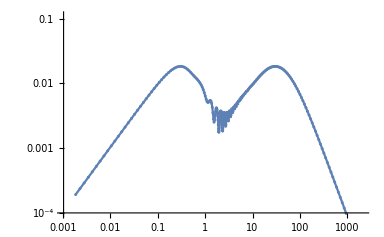

```mathematica
BetaRight = ListLogLogPlot[Table[{kdependence[[1]][[n]][[1]],(√Evaluate[Abs[kdependence[[1]][[n]][[2]][[6]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[7]]]^2+Abs[chiralDOTnsuD[[i]][[8]]]^2,{i,1,4}]+Abs[kdependence[[1]][[n]][[2]][[7]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[5]]]^2+Abs[chiralDOTnsuD[[i]][[6]]]^2,{i,1,4}]/.k0->NN[n]])/2},{n,1,maxN-minN}],PlotMarkers->{Automatic,3}, Joined->True,PlotRange->{10^-4,1/9}]
```

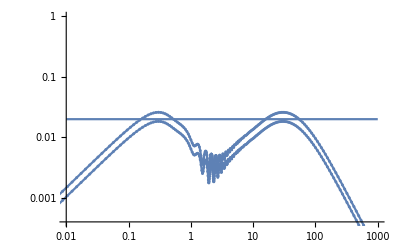

```mathematica
Show[a,BetaLeft, BetaRight]
```

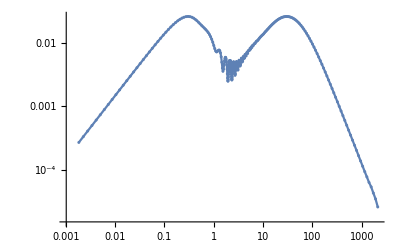

```mathematica
BetaLeft = ListLogLogPlot[Table[{kdependence[[1]][[n]][[1]],(√Evaluate[Abs[kdependence[[1]][[n]][[2]][[6]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[7]]]^2+Abs[chiralDOTnsuD[[i]][[8]]]^2,{i,5,8}]+Abs[kdependence[[1]][[n]][[2]][[7]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[5]]]^2+Abs[chiralDOTnsuD[[i]][[6]]]^2,{i,5,8}]/.k0->NN[n]])/(√2)},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True]
```

```mathematica
Abs[kdependence[[1]][[10]][[2]][[6]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[7]]]^2+Abs[chiralDOTnsuD[[i]][[8]]]^2,{i,1,4}]+Abs[kdependence[[1]][[10]][[2]][[7]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[5]]]^2+Abs[chiralDOTnsuD[[i]][[6]]]^2,{i,1,4}]
```

4.7237×10^-7 (Abs[(√((-k0+√(62500.+k0^2)) (0.+1/2 √(312500.+4 (0.+k0^2-250. √(62500.+k0^2))))))/(√(√(62500.+k0^2) √(312500.+4 (0.+k0^2-250. √(62500.+k0^2)))))]^2+Abs[(√((k0+√(62500.+k0^2)) (0.+1/2 √(312500.+4 (0.+k0^2-250. √(62500.+k0^2))))))/(√(√(62500.+k0^2) √(312500.+4 (0.+k0^2-250. √(62500.+k0^2)))))]^2)+4.23225×10^-6 (Abs[(√((-k0+√(62500.+k0^2)) (0.+1/2 √(312500.+4 (0.+k0^2+250. √(62500.+k0^2))))))/(√(√(62500.+k0^2) √(312500.+4 (0.+k0^2+250. √(62500.+k0^2)))))]^2+Abs[(√((k0+√(62500.+k0^2)) (0.+1/2 √(312500.+4 (0.+k0^2+250. √(62500.+k0^2))))))/(√(√(62500.+k0^2) √(312500.+4 (0.+k0^2+250. √(62500.+k0^2)))))]^2)

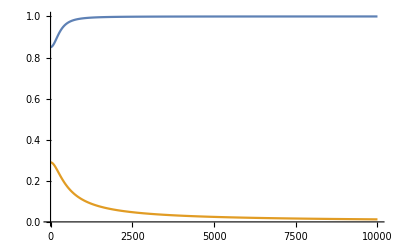

```mathematica
Plot[{PR6[k],PR8[k]},{k,0,10000}]
```

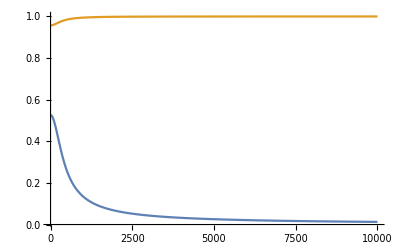

```mathematica
Plot[{PL6[k],PL8[k]},{k,0,10000},PlotRange->All]
```

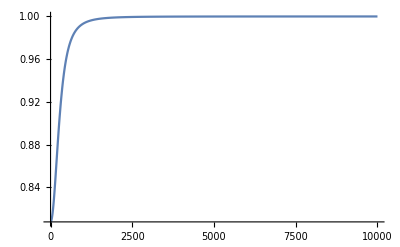

```mathematica
Plot[PR6[k]^2+PR8[k]^2,{k,0,10000},PlotRange->All]
```

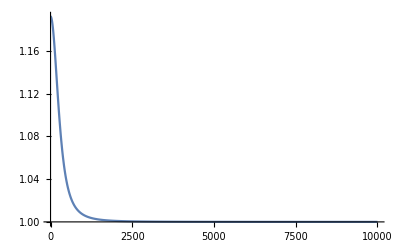

```mathematica
Plot[PL6[k]^2+PL8[k]^2,{k,0,10000},PlotRange->All]
```

```mathematica
a[k_]:=Evaluate[Assuming[k>0&&f[η]>0&&ω3>M[η]&&ω4>M[η] && M[η]>0,FullSimplify[Norm[PL.nsuD[[6]] + PL.nsuD[[8]]]]]/.ω4->ωDc[k,MM/η,FF/η][[8]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
b[k_]:=Evaluate[Assuming[k>0&&f[η]>0&&ω3>M[η]&&ω4>M[η] && M[η]>0,FullSimplify[Norm[PR.nsuD[[6]] + PR.nsuD[[8]]]]]/.ω4->ωDc[k,MM/η,FF/η][[8]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
```

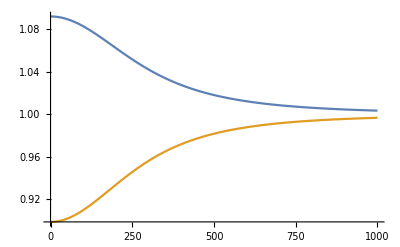

```mathematica
Plot[{a[k],b[k]},{k,0,1000}]
```

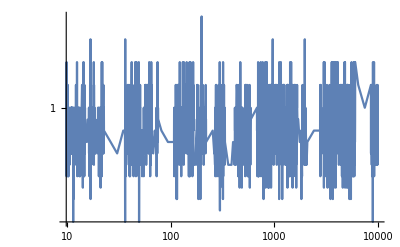

```mathematica
LogLogPlot[PR6[k]^2+ PL6[k]^2,{k,0,10000},PlotRange->All]
```

```mathematica
Evaluate[Abs[kdependence[[1]][[10]][[2]][[6]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[7]]]^2+Abs[chiralDOTnsuD[[i]][[8]]]^2,{i,1,4}]+Abs[kdependence[[1]][[10]][[2]][[7]]]^2*Sum[Abs[chiralDOTnsuD[[i]][[5]]]^2+Abs[chiralDOTnsuD[[i]][[6]]]^2,{i,1,4}],k0->NN[10]]
```

Sequence[4.7237×10^-7 (Abs[(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))-(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))]^2+Abs[(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))+(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))]^2+Abs[(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))-(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))]^2+Abs[(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))+(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(2 √2 √(ω3 √(k^2+f[η]^2)))]^2)+4.23225×10^-6 (Abs[-(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))+(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))]^2+Abs[(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))+(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))]^2+Abs[-(√((k+√(k^2+f[η]^2)) (ω4-M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))-(√((k+√(k^2+f[η]^2)) (ω4+M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))]^2+Abs[(√((k+√(k^2+f[η]^2)) (ω4-M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))-(√((k+√(k^2+f[η]^2)) (ω4+M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))]^2),k0→10.4091]

```mathematica
Abs[chiralDOTnsuD[[2]][[7]]]^2
```

Abs[-(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))+(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(2 √2 √(ω4 √(k^2+f[η]^2)))]^2

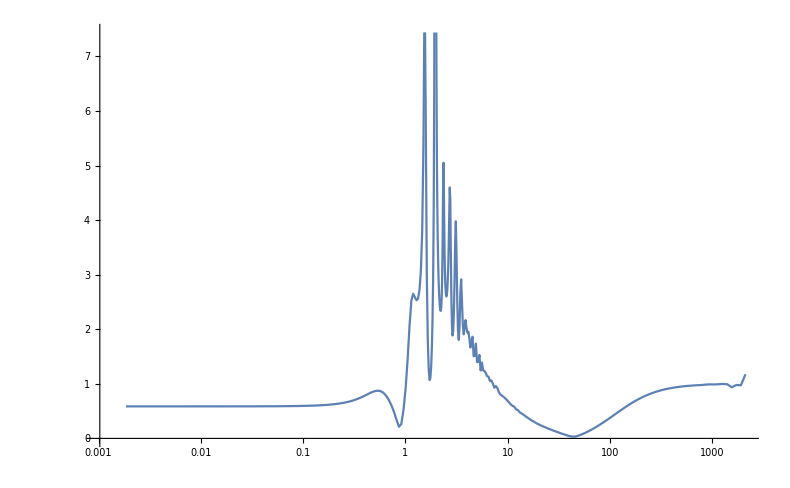

```mathematica
ListLogLinearPlot[Table[{kdependence[[1]][[n]][[1]],Abs[kdependence[[2]][[n]][[2]][[6]]]/Abs[kdependence[[1]][[n]][[2]][[6]]]},{n,1,maxN-minN}], Joined->True]
```